# Introdução à Física Computacional I (2023.2)

## Aula 4: solução de equações algébricas; derivadas; integrais Capítulos 2.2.8, 2.2.9 e 2.2.10

## Solução de equações algébricas

O Mathematica é capaz de fornecer soluções analíticas (quando existem) ou numéricas para equações algébricas.

Antes de discutirmos as funções pertinentes, vale chamar a atenção para como definimos uma equação no Mathematica. Em lugar da igualdade simples, que é reservada para atribuições, utilizamos “==”, como no exemplo abaixo:

```mathematica
2*x+5==3
```

5+2 x==3

A função Solve tenta obter soluções analíticas de equações algébricas:

```mathematica
Solve[x^2-3*x-10==0,x] (* Busca a solução de uma equação em x. *)
```

{{x→-2},{x→5}}

Note que Solve fornece uma “lista aninhada” (lista de listas) de atribuições temporárias (também chamadas de “regras de transformação”). Isso permite que realizemos cálculos com as soluções, utilizando o operador de substituição “/.”. Por exemplo, vamos verificar que de fato se trata de soluções corretas:

```mathematica
x^2-3*x-10==0/.%
```

{True,True}

Tanto as equações quanto as soluções podem ser “valores” atribuídos a variáveis, o que evita ter que explicitamente repetir expressões ou fazer referência a saídas anteriores:

```mathematica
eq1=x^2-3*x-10==0;  (*guarde equações em variáveis*)
```

```mathematica
sols1=Solve[eq1,x]  (*as soluções também em listas é uma estratéia legal*)
```

{{x→-2},{x→5}}

```mathematica
eq1/.sols1
```

{True,True}

Embora funcione principalmente com equações polinomiais (até quarto grau), Solve também pode encontrar soluções de alguns outros tipos de equação. Por exemplo, se quisermos expressar a velocidade de uma partícula em termos de seu momento relativístico:

```mathematica
Solve[p==m*v/Sqrt[1-v^2/c^2],v]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{v→-(c p)/(√(c^2 m^2+p^2))},{v→(c p)/(√(c^2 m^2+p^2))}}

Como apenas a solução com sinal positivo interessa (por quê?), podemos selecioná-la com o auxílio da função Last, que recupera o último elemento de uma lista:

```mathematica
Last[%]
```

{v→(c p)/(√(c^2 m^2+p^2))}

Mais um exemplo, agora com uma equação envolvendo funções trigonométricas:

```mathematica
eq2=9*Cos[x]^2+8*Cos[x]==1;
```

```mathematica
sols2=Solve[eq2,x]
```

{{x→ConditionalExpression[-π+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[π+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[-ArcCos[1/9]+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[ArcCos[1/9]+2 π C[1], C[1]∈ℤ]}}

Note a presença de expressões condicionais nas soluções. Discutiremos condicionais em aulas futuras. Em todo caso, podemos verificar que as soluções são corretas dentro das condições indicadas.

```mathematica
Simplify[eq2/.sols2]
```

{ConditionalExpression[True, C[1]∈ℤ],ConditionalExpression[True, C[1]∈ℤ],ConditionalExpression[True, C[1]∈ℤ],ConditionalExpression[True, C[1]∈ℤ]}

A função Solve também sabe lidar com sistemas de equações:

Para isso, as equações são armazenadas em uma lista e as variáveis de interesse em outra.

```mathematica
Solve[{x+y==z,10-6*x-2*z==0,6*x-24-4*y==0},{x,y,z}]
```

{{x→2,y→-3,z→-1}}

Note que nesse caso tanto o conjunto de equações quanto o conjunto de incógnitas devem ser informados como listas.

### Exemplo: correntes em um circuito elétrico

-Graphics-

Vamos determinar as correntes em termos das demais grandezas. Pelas leis de Kirchoff, temos:

```mathematica
eq1=i1==i2+i3;  
eq2=V==i1*R1+i2*R2; (* V, R1 e R2 não são palavras reservadas! *)
eq3=V==i1*R1+i3*R3;
```

```mathematica
sols=Solve[{eq1,eq2,eq3},{i1,i2,i3}]
```

{{i1→-(-R2 V-R3 V)/(R1 R2+R1 R3+R2 R3),i2→(R3 V)/(R1 R2+R1 R3+R2 R3),i3→(R2 V)/(R1 R2+R1 R3+R2 R3)}}

Vamos testar alguns casos particulares

Se R3=0:

```mathematica
sols/.{R3->0}
```

{{i1→V/R1,i2→0,i3→V/R1}}

Se R2=0:

```mathematica
sols/.{R2->0}
```

{{i1→V/R1,i2→V/R1,i3→0}}

Se R1=0 e R2=R3=R:

```mathematica
sols/.{R1->0,R2-> R,R3-> R}
```

{{i1→(2 V)/R,i2→V/R,i3→V/R}}

Equações polinomiais de grau mais alto podem ser resolvidas numericamente com a função NSolve:

```mathematica
NSolve[x^6-3*x^4+2*x^3+x==4,x]
```

{{x→-2.07229},{x→-0.558743-0.795247 ⅈ},{x→-0.558743+0.795247 ⅈ},{x→0.857131-0.806356 ⅈ},{x→0.857131+0.806356 ⅈ},{x→1.47551}}

Você pode restringir as soluções ao conjunto dos números reais:

```mathematica
NSolve[x^6-3*x^4+2*x^3+x==4,x,Reals]
```

{{x→-2.07229},{x→1.47551}}

Finalmente, um exemplo envolvendo a solução numérica de um sistema de equações:

```mathematica
NSolve[{x^2-x*y-y^2==1,x^3+3*x*y-y^3==9},{x,y}]
```

{{x→-2.07194-1.87447 ⅈ,y→-1.16444-1.26905 ⅈ},{x→-2.07194+1.87447 ⅈ,y→-1.16444+1.26905 ⅈ},{x→1.74511,y→0.802781},{x→-0.43195+0.816763 ⅈ,y→0.552813-1.71762 ⅈ},{x→-0.43195-0.816763 ⅈ,y→0.552813+1.71762 ⅈ},{x→1.76268,y→-2.57952}}

Raízes de equações mais complicadas podem ser obtidas com o auxílio da função FindRoot, cuja discussão fica para uma aula futura.

## Derivadas

Derivadas parciais são obtidas no Mathematica com a função D:

```mathematica
D[x^2,x] (* Neste caso, é claro, trata-se da derivada ordinária. *)
```

2 x

```mathematica
D[Cos[a*x]/(1-Sin[a*x]),x]
```

(a Cos[a x]^2)/(1-Sin[a x])^2-(a Sin[a x])/(1-Sin[a x])

```mathematica
Together[%]
```

(a (Cos[a x]^2-Sin[a x]+Sin[a x]^2))/(-1+Sin[a x])^2

```mathematica
FullSimplify[%]
```

a/(1-Sin[a x])

```mathematica
%/.x-> 0
```

a

Podemos obter derivadas parciais de ordem superior. Por exemplo, para obter a derivada de quarta ordem (∂^4 f)/(∂x^4):, onde a variável de derivação a a ordem são guardados dentro da mesma lista

```mathematica
D[4*x^2-5*x+8-3/x,{x,4}]
```

-72/x^5

```mathematica
D[x^2 + y^2,{x,2}]
```

2

```mathematica
D[4*x^2-5*x+8-3/x,{x,4}] /.x-> 2
```

-9/4

```mathematica
D[(4*x^2-5*x+8-3/x)/.x-> 2,{x,4}]
```

0

No caso de funções de uma só variável, é possível utilizar uma notação compacta com uma aspa:

```mathematica
g[x_]:=Sin[x]+x^2;
```

```mathematica
g'[x]
```

2 x+Cos[x]

Com essa notação, o valor da derivada em um ponto específico, digamos x=π/3, pode ser obtido diretamente:

```mathematica
g'[π/3]
```

1/2+(2 π)/3

A notação se estende a derivadas de ordem superior:

```mathematica
g''[x]  
g'''[x]
g''''[x]
```

2-Sin[x]

-Cos[x]

Sin[x]

Obtendo a derivada cruzada (∂^2 f)/(∂x∂y) de uma função de várias variáveis:

```mathematica
D[(x^3)*(y^2)-2*(x^2)*y+3*x,x,y]
```

-4 x+6 x^2 y

Obtendo a derivada cruzada (∂^5 f)/(∂x^3∂y^2) de uma função de várias variáveis:

```mathematica
D[(x^3)*(y^2)-2*(x^2)*y+3*x,{x,3},{y,2}]
```

12

```mathematica
D[(x^3)*(y^2)-2*(x^2)*y+3*x,x,x,x,y,y]
```

12

Por outro lado, derivadas totais são obtidas por meio da função Dt. Por exemplo, se z=x^2 y+3x y^4 , com x, y e z funções de t, a derivada total de z  com respeito a t pode ser calculada da seguinte maneira:

```mathematica
z=(x^2)*y+3*x*y^4;
Dt[z,t]
```

2 x y Dt[x,t]+3 y^4 Dt[x,t]+x^2 Dt[y,t]+12 x y^3 Dt[y,t]

Se, por exemplo, tivermos x=sin(2t) e y=cos(t), então

```mathematica
Dt[z,t]/.{x-> Sin[2*t],y-> Cos[t]}
```

6 Cos[t]^4 Cos[2 t]+4 Cos[t] Cos[2 t] Sin[2 t]-12 Cos[t]^3 Sin[t] Sin[2 t]-Sin[t] Sin[2 t]^2

Se quisermos calcular a derivada em t=0:

```mathematica
Dt[z,t]/.{x-> Sin[2*t],y-> Cos[t]}/.t-> 0
```

6

Um segundo exemplo. Dada a equação de um círculo, x^2+y^2=25, podemos calcular a derivada de y com respeito a x da seguinte maneira:

```mathematica
Dt[x^2+y^2==25,x]
```

2 x+2 y Dt[y,x]==0

```mathematica
Solve[%,Dt[y,x]]
```

{{Dt[y,x]→-x/y}}

Note que a saída foi dada em termos de uma lista aninhada, mesmo tendo um único elemento. Se quisermos utilizar essa saída para uma regra de transformação, temos que remover a duplicação das chaves, o que pode ser feito com [[1]] ou com a função First. Por exemplo, se quisermos determinar a inclinação da reta tangente ao círculo  no ponto (3,4), podemos fazer

```mathematica
m=Dt[y,x]/.First[%]/.{x-> 3,y-> 4}
```

ReplaceAll::reps: {4+m (-3+x)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Dt::ivar: 3 is not a valid variable.

ReplaceAll::reps: {4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Dt[4,3]/.4

Com isso, a equação da reta tangente ao círculo nesse ponto poderia ser escrita explicitamente:

```mathematica
Simplify[y-4==m*(x-3)]
```

y==4+(-3+x) (Dt[4,3]/.4)

Para evitar fazer repetidas referências à saída anterior (%), podemos colocar em uma única linha uma combinação de comandos, encadeando regras de transformação, embora isso possa inicialmente parecer confuso:

```mathematica
Clear[m]  
Simplify[y-4==m*(x-3)/.{m->Dt[y,x]/.First[Solve[Dt[x^2+y^2==25,x],Dt[y,x]]]/.{x-> 3,y-> 4} }]
```

3 x+4 y==25

Podemos ir ainda um passo adiante e calcular a reta tangente a um ponto qualquer (x_0,y_0), especificado por uma única regra de transformação:

```mathematica
Simplify[y-y0==m*(x-x0)/.{m->Dt[y,x]/.First[Solve[Dt[x^2+y^2==25,x],Dt[y,x]]]/.{x-> x0,y-> y0} }/.{x0-> 3,y0-> 4}]
```

3 x+4 y==25

```mathematica
Simplify[y-y0==m*(x-x0)/.{m->Dt[y,x]/.First[Solve[Dt[x^2+y^2==25,x],Dt[y,x]]]/.{x-> x0,y-> y0} }/.{x0-> 0,y0-> 5}]
```

y==5

```mathematica
Simplify[y-y0==m*(x-x0)/.{m->Dt[y,x]/.First[Solve[Dt[x^2+y^2==25,x],Dt[y,x]]]/.{x-> x0,y-> y0} }/.{{x0-> 0,y0-> 5},{x0-> 3,y0-> 4}}]
```

{y==5,3 x+4 y==25}

Caso o problema envolva parâmetros que devem permanecer constantes ao se tomar a derivada total, podemos fazer uso da função SetAttributes:

```mathematica
SetAttributes[{a,b},Constant]
```

```mathematica
Dt[a*x^2+b*y^2==25,x]
```

2 a x+2 b y Dt[y,x]==0

```mathematica
Solve[%,Dt[y,x]]
```

{{Dt[y,x]→-(a x)/(b y)}}

```mathematica
ClearAttributes[{a,b},Constant] (* Vamos desfazer o atributo *)
```

## Integração

Integrais indefinidas e definidas (quando existirem formas analíticas fechadas) podem ser feitas com a função Integrate.

Para calcular uma integral indefinida na variável x (note a ausência, na saída, de uma constante arbitrária):

```mathematica
Integrate[x^4/(a^2+x^2),x]
```

-a^2 x+x^3/3+a^3 ArcTan[x/a]

Agora uma integral definida entre x=0 e x=a deve ser alocada em uma lista com a variável de integração.

```mathematica
Integrate[x^4/(a^2+x^2),{x,0,a}]
```

1/12 a^3 (-8+3 π)

A função Integrate aceita suposições indicadas pela opção Assumptions, como no exemplo abaixo:

```mathematica
Integrate[Sin[x]^p,{x,0,π},Assumptions-> Re[p]>-1]
```

(√π Gamma[(1+p)/2])/Gamma[1+p/2]

Também é possível inverter a ordem e utilizar Integrate como argumento da função Assuming, como nestes outros exemplos, que envolvem a integral ∫_0^(2π) sin(m x)sin(n x)dx:

```mathematica
Integrate[Sin[m*x]*Sin[n*x],{x,0,2*π}]
```

(n Cos[2 n π] Sin[2 m π]-m Cos[2 m π] Sin[2 n π])/(m^2-n^2)

```mathematica
Assuming[m∈NonNegativeIntegers && n∈NonNegativeIntegers&&m≠n,Integrate[Sin[m*x]*Sin[n*x],{x,0,2*π}]]
```

0

```mathematica
Assuming[m∈NonNegativeIntegers && n∈NonNegativeIntegers&&m==n,Integrate[Sin[m*x]*Sin[n*x],{x,0,2*π}]]
```

π

Integrais múltiplas são feitas com a sintaxe do exemplo abaixo, que corresponde à expressão ∫_0^1 dx∫_0^(√(1-x^2)) dy √(1-x^2-y^2), fornecendo o volume de um octante de uma esfera de raio unitário:

```mathematica
Integrate[Sqrt[1-x^2-y^2],{x,0,1},{y,0,Sqrt[1-x^2]}]
```

π/6

Note que as variáveis de integração são varridas na ordem da apresentação dos argumentos. No exemplo, a varredura em x é feita primeiro, e a varredura em y é feita por último. Como o limite superior da integral em y depende de x, inverter os argumentos causaria problemas.

Integrais que o Mathematica não consegue calcular de forma fechada podem ser aproximadas numericamente com a função NIntegrate:

```mathematica
NIntegrate[Sin[Sqrt[1+x^4+Sin[x^3]]],{x,0,2}]
```

1.31859

Os métodos de integração utilizados são descritos na documentação. Vários deles envolvem aproximar a integração por uma soma sobre intervalos de largura adaptável, verificando a convergência à medida que a discretização é refinada. Mais sobre esses métodos na disciplina de Cálculo Numérico.

Integrais múltiplas também podem ser calculadas, como no exemplo abaixo, relevante para o cálculo do potencial elétrico, em um ponto qualquer, produzido por um disco uniformemente carregado de raio a, centrado na origem e perpendicular ao eixo z. Se (x,y,z)  são as coordenadas do ponto, a integral relevante, em coordenadas cilíndricas, é

∫_0^a dr∫_0^(2π) dϕr/(√((x-r cos ϕ)^2+(y-r sin ϕ)^2+z^2)).

(O potencial elétrico corresponde à integral multiplicada por σ/4 πϵ_0.) Se quisermos manter o valor de a como variável, podemos definir uma função V(a,x,y,z) que forneça o valor da integral:

```mathematica
V[a_,x_,y_,z_]:=NIntegrate [r/Sqrt[(x-r*Cos[ϕ])^2+(y-r*Sin[ϕ])^2+z^2],{r,0,a},{ϕ,0,2*π}]
```

Em seguida, podemos utilizar a função para calcular o potencial nos pontos que desejarmos. Por exemplo:

```mathematica
V[1,1,2,5]
```

0.570012

Podemos inclusive fazer gráficos do potencial como função de uma das coordenadas. Vamos calcular o potencial ao longo do eixo perpendicular ao disco (nesse caso há uma solução analítica fechada, que você pode obter pela função Integrate):

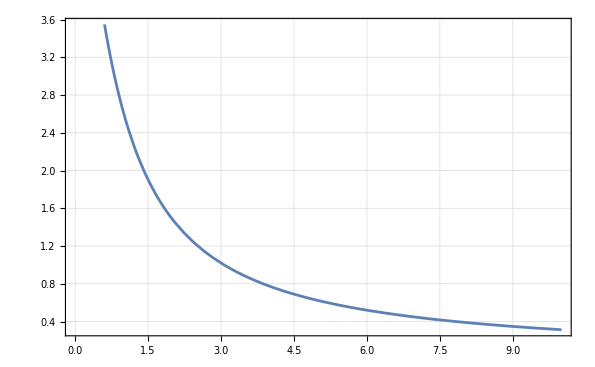

```mathematica
Plot[V[1,0,0,z],{z,0,10}, GridLines->Automatic, Frame->True]
```

O comportamento do potencial a grandes distâncias do disco corresponde ao de uma carga puntiforme na origem, como esperado:

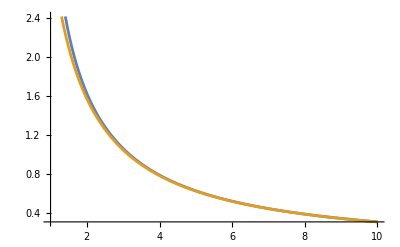

```mathematica
Plot[{V[1,x,0,0],π/x},{x,1,10}]
```

## Exercícios no E-disciplinas